```mathematica
(* RSA toy parameters *)
p = Prime[6]
q = Prime[8]
n = p q
e = Prime[10]
d = PowerMod[e,-1,(p-1)(q-1)]
(* function which returns first bit of an 8-bit number *)
firstbit[nn_] = (1+Sign[nn-127.5])/2;
```

```mathematica
unknownmsg = 181;
BaseForm[unknownmsg,2]
c = PowerMod[unknownmsg, e, n]
PowerMod[c,d,n]
```

```mathematica
(* oracle *) 
cx = Mod[c* PowerMod[2^Range[1,8],e,n],n]
oracle = firstbit[PowerMod[cx,d,n]]
plaintext = firstbit[Mod[unknownmsg*2^Range[1,8],n]]
```

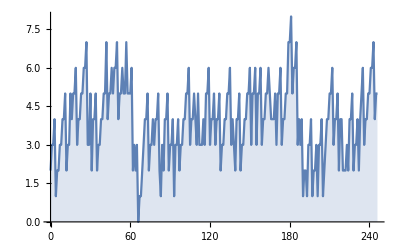

```mathematica
DiscretePlot[
{1-Abs[firstbit[Mod[i*2,n]]-oracle[[1]]]}+
{1-Abs[firstbit[Mod[i*4,n]]-oracle[[2]]]}+
{1-Abs[firstbit[Mod[i*8,n]]-oracle[[3]]]}+
{1-Abs[firstbit[Mod[i*16,n]]-oracle[[4]]]}+
{1-Abs[firstbit[Mod[i*32,n]]-oracle[[5]]]} +
{1-Abs[firstbit[Mod[i*64,n]]-oracle[[6]]]}+
{1-Abs[firstbit[Mod[i*128,n]]-oracle[[7]]]}+
{1-Abs[firstbit[Mod[i*256,n]]-oracle[[8]]]}
, {i,0,246}]
```

```mathematica
For[i=0,i<n,i++,Print[i,"-->",firstbit[Mod[2i,n]],firstbit[Mod[4i,n]]]]
```